```mathematica
target[x_]:=1+5x+3x^2
range={-10, 10, 0.01};
```

```mathematica
xVals=Range@@range;
funcFromVals[vals_][x_]:=Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], {InterpolatingFunction::dmval, InterpolatingFunction::dprec}]
```

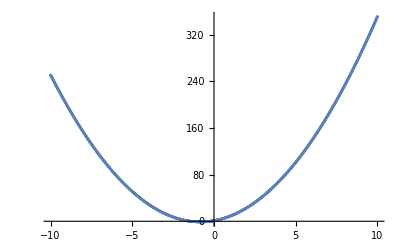

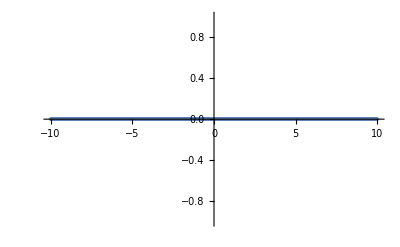

```mathematica
approxVals=(0&)/@xVals;
funcVals=target/@xVals;

PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}]], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}]}]

PlotVals[funcVals]
PlotVals[approxVals]

plots={};
```

```mathematica
imax=10;jmax=5;

progress=PrintTemporary["0% Complete"];
Table[Table[
approxFunc=funcFromVals[approxVals];
nestedApproxVals=approxFunc[approxFunc[#]]&/@xVals;
deltaVals=funcVals-nestedApproxVals;
newApproxVals=approxVals+0.1*deltaVals;
approxVals=newApproxVals;
NotebookDelete[progress];
progress=PrintTemporary[ToString[Floor[100*(i*jmax+j)/((imax+1)*(jmax+1))]]<>"% Complete"],{j, jmax}];
plots=AppendTo[plots,Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}]];
, {i,imax}];
```

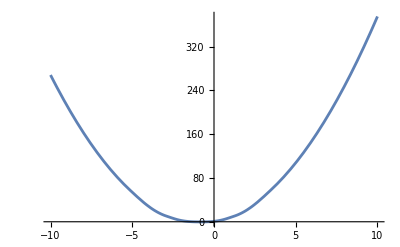
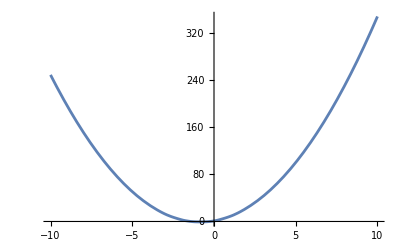
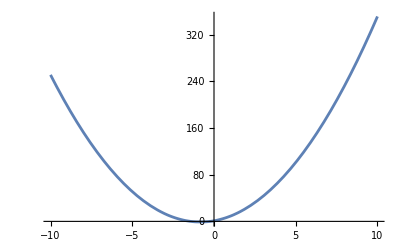
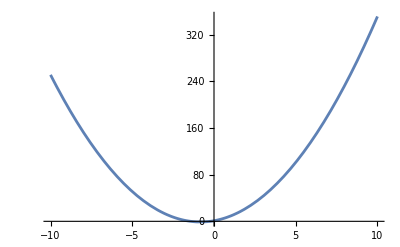
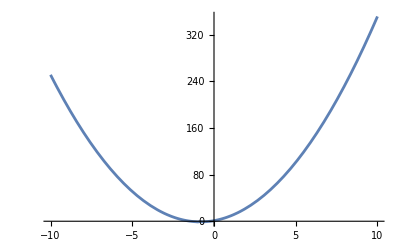
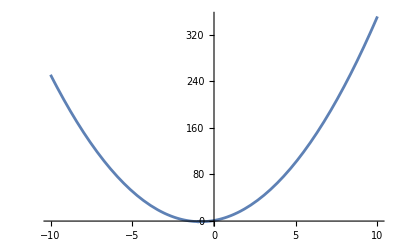
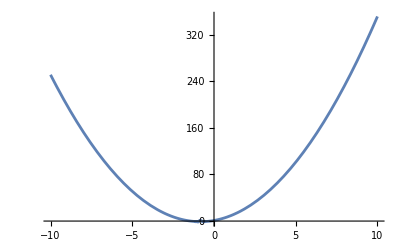
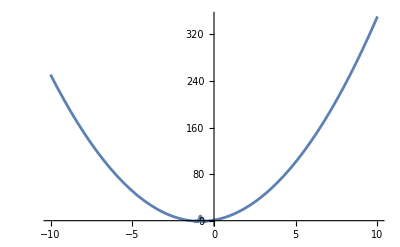

```mathematica
plots
```

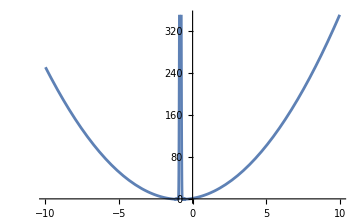
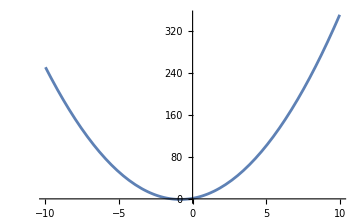
-Graphics-approx-Graphics-target

```mathematica
pTarget=Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->Medium];
pRange=AbsoluteOptions[pTarget,PlotRange][[1,2]];
pApprox=Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Medium, PlotRange->pRange];

Row[{Labeled[pApprox, "approx"], Labeled[pTarget, "target"]}]
```